```mathematica
Table[allGraphs[k,"colofour"],{k,{29602,29440,29446}}]
```

{v1x24x35+v1x24x3x5,v1x24x35+v1x24x3x5+v1x2x35x4+v1x2x3x4x5,v1x24x35+v1x2x35x4}

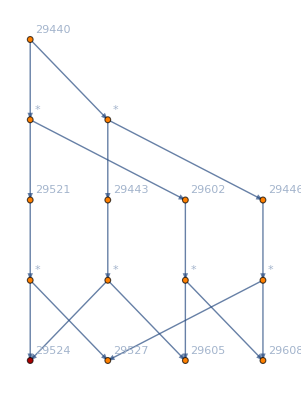

```mathematica
Graph[DependencyGraph[allGraphs,29440],GraphLayout->"LayeredDigraphEmbedding"]
```

```mathematica
CompleteFourBaseCoeff[ ChromaticPolynomial[allGraphs[29521,"graph"],x]]
```

{24,216,312,136,21,1}

```mathematica
CompleteFourBaseCoeff[ ChromaticPolynomial[allGraphs[29527,"graph"],x]]
```

{24,96,72,16,1}

```mathematica
CompleteFourBaseCoeff[ ChromaticPolynomial[allGraphs[29524,"graph"],x]]
```

{0,120,240,120,20,1}

```mathematica
CompleteFourBaseCoeff[ ChromaticPolynomial[EmbedGraph5Plantri8[allGraphs,29521],x]]
```

{144,899736,117023952,2355683136,14326947466,36323666801,46034248402,32619922449,13896029326,3731314022,650304007,74630893,5638748,275476,8314,140,1}

```mathematica
CompleteFourBaseCoeff[ ChromaticPolynomial[EmbedGraph5Plantri8[allGraphs,29527],x]]
```

{144,426696,38137152,575270736,2742891226,5591556779,5776294492,3355661733,1171318028,256035102,35846404,3232256,185121,6454,124,1}

```mathematica
CompleteFourBaseCoeff[ ChromaticPolynomial[EmbedGraph5Plantri8[allGraphs,29524],x]]
```

{0,473040,78886800,1780412400,11584056240,30732110022,40257953910,29264260716,12724711298,3475278920,614457603,71398637,5453627,269022,8190,139,1}

```mathematica
allGraphs[29521,"colofournull"]
```

1/12 (9 p12345+3 p1234x5-p1235x4+3 p123x45-2 p123x4x5+3 p1245x3-9 p124x35+6 p124x3x5+3 p125x34-2 p125x3x4-3 p12x345+4 p12x35x4-2 p12x3x4x5-p1345x2+3 p134x25-2 p134x2x5-3 p135x24+2 p135x2x4+3 p13x245-2 p13x25x4-2 p13x2x45+2 p13x2x4x5+3 p145x23-2 p145x2x3-3 p14x235+4 p14x2x35-2 p14x2x3x5+3 p15x234-2 p15x23x4-2 p15x2x34+2 p15x2x3x4-p1x2345-2 p1x234x5+2 p1x235x4-2 p1x23x45+2 p1x23x4x5-2 p1x245x3+4 p1x24x35-2 p1x24x3x5-2 p1x25x34+2 p1x25x3x4+2 p1x2x345+2 p1x2x34x5-6 p1x2x35x4+2 p1x2x3x45)

```mathematica
Table[
With[
{r=ChromaticPolynomial[EmbedGraph5Plantri8[allGraphs,k],x]
 },
k->PadRight[CompleteFourBaseCoeff[r],20]
],{k,{29602,29446,29521,29443}}]
```

{29602→{144,617016,50429472,714732576,3261972626,6436188925,6480723692,3687107297,1264653339,272307411,37626033,3353314,190049,6563,125,1,0,0,0,0},29446→{144,617016,50429472,714732576,3261972626,6436188925,6480723692,3687107297,1264653339,272307411,37626033,3353314,190049,6563,125,1,0,0,0,0},29521→{144,899736,117023952,2355683136,14326947466,36323666801,46034248402,32619922449,13896029326,3731314022,650304007,74630893,5638748,275476,8314,140,1,0,0,0},29443→{144,899736,117023952,2355683136,14326947466,36323666801,46034248402,32619922449,13896029326,3731314022,650304007,74630893,5638748,275476,8314,140,1,0,0,0}}

```mathematica
Table[allGraphs[k,"colofour"],{k,{36004,22882,23044}}]
```

{v13x24x5+v13x2x4x5,v13x24x5+v13x2x4x5+v1x24x3x5+v1x2x3x4x5,v13x24x5+v1x24x3x5}

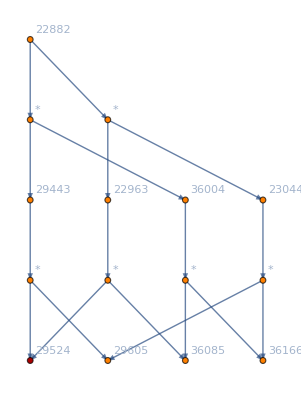

```mathematica
Graph[DependencyGraph[allGraphs,22882],GraphLayout->"LayeredDigraphEmbedding"]
```

```mathematica
Table[
With[
{r=ChromaticPolynomial[EmbedGraph5Plantri8[allGraphs,k],x]
 },
k->PadRight[CompleteFourBaseCoeff[r],20]
],{k,{29443,22963,36004,23044}}]
```

{29443→{144,899736,117023952,2355683136,14326947466,36323666801,46034248402,32619922449,13896029326,3731314022,650304007,74630893,5638748,275476,8314,140,1,0,0,0},22963→{216,917424,117012168,2350780464,14300482929,36275223630,45993322828,32601603706,13891353721,3730608516,650240690,74627609,5638658,275475,8314,140,1,0,0,0},36004→{288,643512,50410824,708605952,3230459972,6380513245,6434984823,3667100373,1259645798,271564548,37560356,3349953,189958,6562,125,1,0,0,0,0},23044→{216,625824,50422608,713508624,3256924509,6428956416,6475910397,3685419116,1264321403,272270054,37623673,3353237,190048,6563,125,1,0,0,0,0}}

```mathematica
sample=ChromaticPolynomial[EmbedGraph5Plantri8[allGraphs,29443],x]
```

-34563084 x+159855992 x^2-338172911 x^3+438416617 x^4-392529281 x^5+258635053 x^6-130147286 x^7+51098897 x^8-15816439 x^9+3863982 x^10-739265 x^11+108756 x^12-11902 x^13+914 x^14-44 x^15+x^16

```mathematica
NullBaseCoeff[sample]
```

{0,-34563084,159855992,-338172911,438416617,-392529281,258635053,-130147286,51098897,-15816439,3863982,-739265,108756,-11902,914,-44,1}

```mathematica
Accumulate[NullBaseCoeff[sample]]
```

{0,-34563084,125292908,-212880003,225536614,-166992667,91642386,-38504900,12593997,-3222442,641540,-97725,11031,-871,43,-1,0}

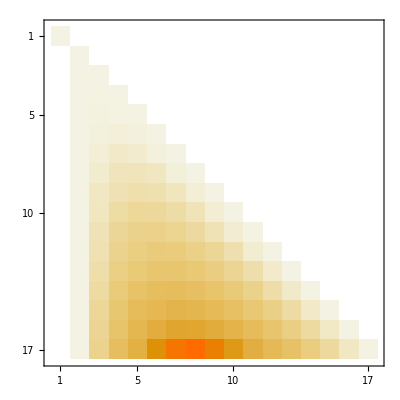

```mathematica
FromNormalToComplete[17]//MatrixPlot
```

```mathematica
With[{mat=NullBaseCoeff[sample]},
Table[Indexed[ζ,k]->mat[[k]],{k,1,17}]
]
```

{ζ1→0,ζ2→-34563084,ζ3→159855992,ζ4→-338172911,ζ5→438416617,ζ6→-392529281,ζ7→258635053,ζ8→-130147286,ζ9→51098897,ζ10→-15816439,ζ11→3863982,ζ12→-739265,ζ13→108756,ζ14→-11902,ζ15→914,ζ16→-44,ζ17→1}

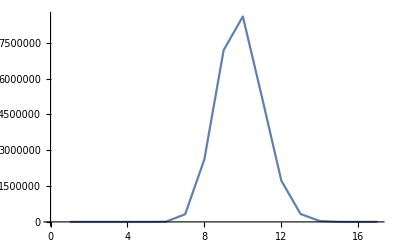

```mathematica
CompleteBaseCoeff[sample]//ListLinePlot
```

```mathematica
Map[#->(#/.{ζ1->0,ζ2->-34563084,ζ3->159855992,ζ4->-338172911,ζ5->438416617,ζ6->-392529281,ζ7->258635053,ζ8->-130147286,ζ9->51098897,ζ10->-15816439,ζ11->3863982,ζ12->-739265,ζ13->108756,ζ14->-11902,ζ15->914,ζ16->-44,ζ17->1})&,Table[Indexed[ζ,i],{i,1,17}].FromNormalToComplete[17]]//TableForm
```

ζ1→0
ζ2+ζ3+ζ4+ζ5+ζ6+ζ7+ζ8+ζ9+ζ10+ζ11+ζ12+ζ13+ζ14+ζ15+ζ16+ζ17→0
ζ3+3 ζ4+7 ζ5+15 ζ6+31 ζ7+63 ζ8+127 ζ9+255 ζ10+511 ζ11+1023 ζ12+2047 ζ13+4095 ζ14+8191 ζ15+16383 ζ16+32767 ζ17→0
ζ4+6 ζ5+25 ζ6+90 ζ7+301 ζ8+966 ζ9+3025 ζ10+9330 ζ11+28501 ζ12+86526 ζ13+261625 ζ14+788970 ζ15+2375101 ζ16+7141686 ζ17→0
ζ5+10 ζ6+65 ζ7+350 ζ8+1701 ζ9+7770 ζ10+34105 ζ11+145750 ζ12+611501 ζ13+2532530 ζ14+10391745 ζ15+42355950 ζ16+171798901 ζ17→6
ζ6+15 ζ7+140 ζ8+1050 ζ9+6951 ζ10+42525 ζ11+246730 ζ12+1379400 ζ13+7508501 ζ14+40075035 ζ15+210766920 ζ16+1096190550 ζ17→7493
ζ7+21 ζ8+266 ζ9+2646 ζ10+22827 ζ11+179487 ζ12+1323652 ζ13+9321312 ζ14+63436373 ζ15+420693273 ζ16+2734926558 ζ17→320070
ζ8+28 ζ9+462 ζ10+5880 ζ11+63987 ζ12+627396 ζ13+5715424 ζ14+49329280 ζ15+408741333 ζ16+3281882604 ζ17→2620417
ζ9+36 ζ10+750 ζ11+11880 ζ12+159027 ζ13+1899612 ζ14+20912320 ζ15+216627840 ζ16+2141764053 ζ17→7183354
ζ10+45 ζ11+1155 ζ12+22275 ζ13+359502 ζ14+5135130 ζ15+67128490 ζ16+820784250 ζ17→8598282
ζ11+55 ζ12+1705 ζ13+39325 ζ14+752752 ζ15+12662650 ζ16+193754990 ζ17→5200955
ζ12+66 ζ13+2431 ζ14+66066 ζ15+1479478 ζ16+28936908 ζ17→1729069
ζ13+78 ζ14+3367 ζ15+106470 ζ16+2757118 ζ17→330276
ζ14+91 ζ15+4550 ζ16+165620 ζ17→36692
ζ15+105 ζ16+6020 ζ17→2314
ζ16+120 ζ17→76
ζ17→1

```mathematica
Reduce[ζ2+ζ3+ζ4+ζ5+ζ6+ζ7+ζ8+ζ9+ζ10+ζ11+ζ12+ζ13+ζ14+ζ15+ζ16+ζ17==0&&ζ3+3 ζ4+7 ζ5+15 ζ6+31 ζ7+63 ζ8+127 ζ9+255 ζ10+511 ζ11+1023 ζ12+2047 ζ13+4095 ζ14+8191 ζ15+16383 ζ16+32767 ζ17==0&&ζ4+6 ζ5+25 ζ6+90 ζ7+301 ζ8+966 ζ9+3025 ζ10+9330 ζ11+28501 ζ12+86526 ζ13+261625 ζ14+788970 ζ15+2375101 ζ16+7141686 ζ17==0&&ζ5+10 ζ6+65 ζ7+350 ζ8+1701 ζ9+7770 ζ10+34105 ζ11+145750 ζ12+611501 ζ13+2532530 ζ14+10391745 ζ15+42355950 ζ16+171798901 ζ17>0&&ζ6+15 ζ7+140 ζ8+1050 ζ9+6951 ζ10+42525 ζ11+246730 ζ12+1379400 ζ13+7508501 ζ14+40075035 ζ15+210766920 ζ16+1096190550 ζ17>0&&ζ7+21 ζ8+266 ζ9+2646 ζ10+22827 ζ11+179487 ζ12+1323652 ζ13+9321312 ζ14+63436373 ζ15+420693273 ζ16+2734926558 ζ17>0&&ζ17==1&&ζ16+120 ζ17>0,{ζ2,ζ3,ζ4,ζ5}]
```

(ζ7|ζ8|ζ9|ζ10|ζ11|ζ12|ζ13|ζ14)∈Reals&&((ζ15≤(47748266202-ζ7-21 ζ8-266 ζ9-2646 ζ10-22827 ζ11-179487 ζ12-1323652 ζ13-9321312 ζ14)/63436373&&ζ16>(-2734926558-ζ7-21 ζ8-266 ζ9-2646 ζ10-22827 ζ11-179487 ζ12-1323652 ζ13-9321312 ζ14-63436373 ζ15)/420693273&&ζ6>-1096190550-15 ζ7-140 ζ8-1050 ζ9-6951 ζ10-42525 ζ11-246730 ζ12-1379400 ζ13-7508501 ζ14-40075035 ζ15-210766920 ζ16&&ζ17==1&&Re[ζ2]<1016542800+24 ζ6+240 ζ7+1560 ζ8+8400 ζ9+40824 ζ10+186480 ζ11+818520 ζ12+3498000 ζ13+14676024 ζ14+60780720 ζ15+249401880 ζ16&&Im[ζ2]==0&&ζ3==1/6 (-28402920-36 ζ6-216 ζ7-900 ζ8-3240 ζ9-10836 ζ10-34776 ζ11-108900 ζ12-335880 ζ13-1026036 ζ14-3114936 ζ15-9418500 ζ16-11 Re[ζ2])&&ζ4==1/4 (32760+8 ζ6+24 ζ7+56 ζ8+120 ζ9+248 ζ10+504 ζ11+1016 ζ12+2040 ζ13+4088 ζ14+8184 ζ15+16376 ζ16-7 Re[ζ2]-6 Re[ζ3]))||(ζ15>(47748266202-ζ7-21 ζ8-266 ζ9-2646 ζ10-22827 ζ11-179487 ζ12-1323652 ζ13-9321312 ζ14)/63436373&&ζ16>-120&&ζ6>-1096190550-15 ζ7-140 ζ8-1050 ζ9-6951 ζ10-42525 ζ11-246730 ζ12-1379400 ζ13-7508501 ζ14-40075035 ζ15-210766920 ζ16&&ζ17==1&&Re[ζ2]<1016542800+24 ζ6+240 ζ7+1560 ζ8+8400 ζ9+40824 ζ10+186480 ζ11+818520 ζ12+3498000 ζ13+14676024 ζ14+60780720 ζ15+249401880 ζ16&&Im[ζ2]==0&&ζ3==1/6 (-28402920-36 ζ6-216 ζ7-900 ζ8-3240 ζ9-10836 ζ10-34776 ζ11-108900 ζ12-335880 ζ13-1026036 ζ14-3114936 ζ15-9418500 ζ16-11 Re[ζ2])&&ζ4==1/4 (32760+8 ζ6+24 ζ7+56 ζ8+120 ζ9+248 ζ10+504 ζ11+1016 ζ12+2040 ζ13+4088 ζ14+8184 ζ15+16376 ζ16-7 Re[ζ2]-6 Re[ζ3])))&&ζ5==-ζ2-ζ3-ζ4-ζ6-ζ7-ζ8-ζ9-ζ10-ζ11-ζ12-ζ13-ζ14-ζ15-ζ16-ζ17

```mathematica
MatrixForm[FromNormalToComplete[17]]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 7 | 6 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 15 | 25 | 10 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 31 | 90 | 65 | 15 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 63 | 301 | 350 | 140 | 21 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 127 | 966 | 1701 | 1050 | 266 | 28 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 255 | 3025 | 7770 | 6951 | 2646 | 462 | 36 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 511 | 9330 | 34105 | 42525 | 22827 | 5880 | 750 | 45 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1023 | 28501 | 145750 | 246730 | 179487 | 63987 | 11880 | 1155 | 55 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 2047 | 86526 | 611501 | 1379400 | 1323652 | 627396 | 159027 | 22275 | 1705 | 66 | 1 | 0 | 0 | 0 | 0
0 | 1 | 4095 | 261625 | 2532530 | 7508501 | 9321312 | 5715424 | 1899612 | 359502 | 39325 | 2431 | 78 | 1 | 0 | 0 | 0
0 | 1 | 8191 | 788970 | 10391745 | 40075035 | 63436373 | 49329280 | 20912320 | 5135130 | 752752 | 66066 | 3367 | 91 | 1 | 0 | 0
0 | 1 | 16383 | 2375101 | 42355950 | 210766920 | 420693273 | 408741333 | 216627840 | 67128490 | 12662650 | 1479478 | 106470 | 4550 | 105 | 1 | 0
0 | 1 | 32767 | 7141686 | 171798901 | 1096190550 | 2734926558 | 3281882604 | 2141764053 | 820784250 | 193754990 | 28936908 | 2757118 | 165620 | 6020 | 120 | 1)